```mathematica
f[x_]:=0.2 + 25x - 200 *x ^2+675*x^3-900*x^4 + 400 * x^5;
```

```mathematica
f[0]
```

0.2

```mathematica
g = Integrate[f, x];
```

```mathematica
g
```

f x

```mathematica
{{g = Integrate[f[x], {x,0,0.8}]}, {□}};
```

```mathematica
g
```

1.64053

```mathematica
a= 0; b=0.8;
```

```mathematica
l = (b-a)* (f[a] + f[b]) / 2;
```

```mathematica
l
```

0.1728

```mathematica
err = -1 / 12 * f''(0.4)(b-a)^3;
```

```mathematica
err
```

-0.0170667 (-400+4050 #1-10800 #1^2+8000 #1^3&)

```mathematica
err = -1 / 12 * f''[0.6]*((b-a)^3);
```

```mathematica
err
```

5.54667

```mathematica
TrapRule[f_, a0_, b0_, m0_] := Module[{a=N[a0], b=N[b0], m=m0, k, s2},
h = (b-a) / m;
sum = 0;
s2 = 0;
For[k=1, k≤ m, k++,
	sum = sum + f[a + h*k];
	s2+= f''[a + h*k - 0.001];
];
Print[- (h^3)/(12 * m^3) * s2];
Return[h/2 * (f[a] + f[b]) + h*sum];
];
```

```mathematica
r = TrapRule[f, a, b, 2];
```

-0.0177515

```mathematica
r
```

1.1616

0.0864

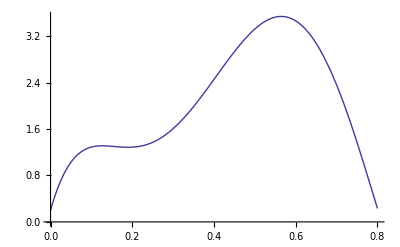

```mathematica
0.08639999999999703

Plot[f[x], {x, a, b}]
```

```mathematica
a1 = 0; b2 = Pi;
```

```mathematica
b2
```

π

```mathematica
a2 = 0;
```

```mathematica
TrapRule2[f_, a0_, b0_] := Module[{a=N[a0], b=N[b0], k, s2, m},
err = 1;
For[m=2, m ≤20, m++,
h = (b-a) / m;
sum = 0;
s2 = 0;
For[k=1, k≤ m, k++,
	sum = sum + f[a + h*k];
	s2+= f''[a + h*k - 0.01];
];
err = - (h^3)/(12 * m^2) * (s2 / m);
Print[m];
Print[err];
If[err ≤ 0.0002, Print[h/2 * (f[a] + f[b]) + h*sum];Break[]];
]
];
```

```mathematica
g[y_] := Sin[y];
```

SetDelayed::write: Tag Real in 1.64053[y_] is Protected.

```mathematica
g[Pi]
```

```mathematica
1.6405333333333516[π]
TrapRule2[Sin, a2, b2];
```

1.64053[π]

2

0.0407745

3

0.00617419

4

0.00152918

5

0.000510575

6

0.000207228

7

0.0000964384

1.96632

```mathematica
Integrate[Sin[x], {x, 0, Pi}]
```

2

```mathematica
h2 = (b2 - a2);
```

```mathematica
Simpsons13[f_, a0_, b0_, n_] := Module[{h=(b0-a0)/n, coeff},
	coeff[i_?EvenQ] = 2;
	coeff[i_?OddQ] = 4;
	Return[N[h/ 3 * (f[a0] + f[b0] +
	 Sum[coeff[i]*f[a0 + i*h], {i, 1, n-1}])]];
];
```

```mathematica
Simpsons13[Sin, 0, Pi,  4]
```

2.00456

```mathematica
Simpsons38[f_, a0_, b0_, n_] := Module[{h=(b0-a0)/3},
	Return[
	N[
		(3*h) / 8 * (f[a0] + f[b0] +
	 Sum[3*f[a0 + i*h], {i, 1, n-1}])
	]
	];
];
```

```mathematica
b = Simpsons38[Sin, 0, Pi, 10];
```

```mathematica
b
```

2.04052